## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
100. | 0. | 1.29819 | 0.501422
1000. | 0. | 48.1539 | 0.322477
2000. | 0. | 98.455 | 0.465343
3000. | 0. | 146.707 | 0.551534
4000. | 0. | 195.453 | 0.648293
5000. | 0. | 245.009 | 0.694895
6000. | 0. | 292.981 | 0.805155
7000. | 0. | 341.44 | 0.82758
8000. | 0. | 391.156 | 0.888588
9000. | 0. | 438.943 | 1.03013
10000. | 0. | 486.366 | 1.03747

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-0.709061+0.0488886 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.709061 | 0.776272 | -0.913419 | 0.384839
x | 0.0488886 | 0.000131212 | 372.592 | 3.67835×10^-20

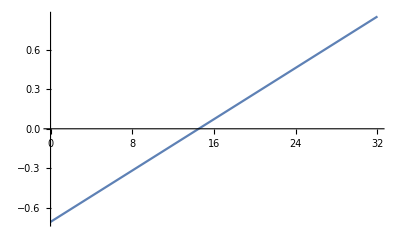

```mathematica
forFit=data⟦2;;,{1,3}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

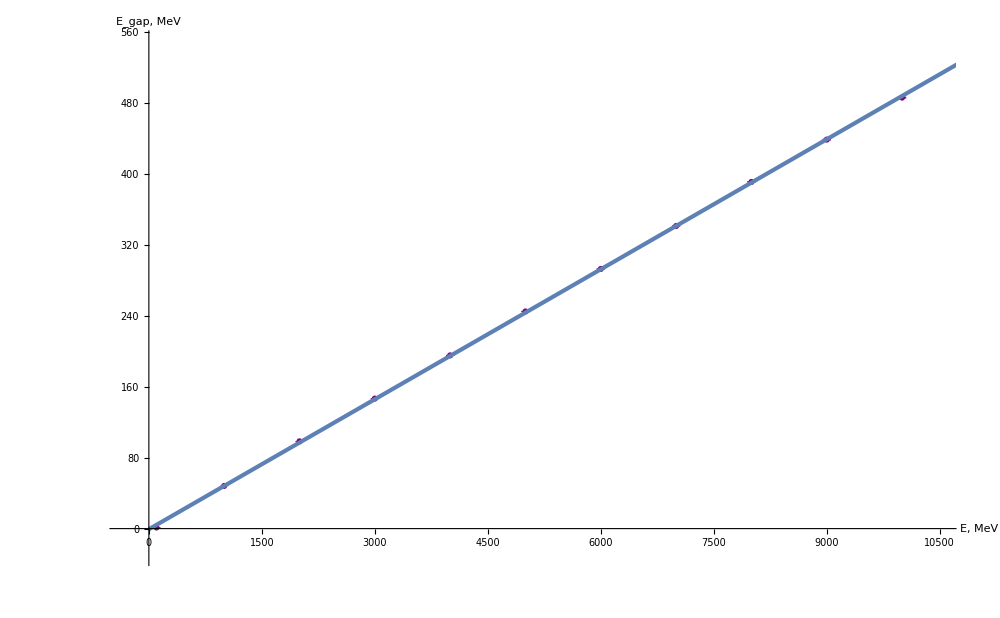

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/calib.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_res.png

```mathematica
plot =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,550}}], 
Plot[fit["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/calib.png",plot,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_res.png",fit@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exp = {fit[0],fit[1]-fit[0]};
exp//TableForm
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res.csv",exp,"CSV"]
```

-0.709061
0.0488886

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
138.604 | 3.39379 | 0.624492 | 0.0245599
551.499 | 4.80344 | 0.275158 | 0.00664344
1027.23 | 6.60544 | 0.203346 | 0.00473155
2973.5 | 11.2232 | 0.119358 | 0.00270658
3541.66 | 11.8488 | 0.105795 | 0.00239196
4141.34 | 13.5926 | 0.103791 | 0.00234577
5031.36 | 14.3962 | 0.0904821 | 0.0020397
6324.43 | 16.6831 | 0.0834173 | 0.00187817
7206.86 | 17.9422 | 0.0787283 | 0.00177126
7999.15 | 19.1061 | 0.0755314 | 0.00169852
9750.33 | 21.2747 | 0.0688258 | 0.00156944

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-0.013518+7.34727/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.013518 | 0.00513593 | -2.63205 | 0.0272666
1/(√x) | 7.34727 | 0.15826 | 46.4255 | 4.99645×10^-12

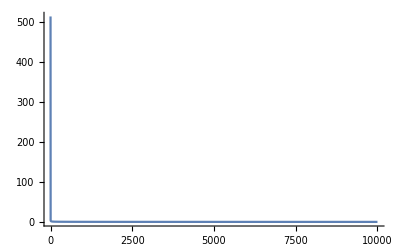

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

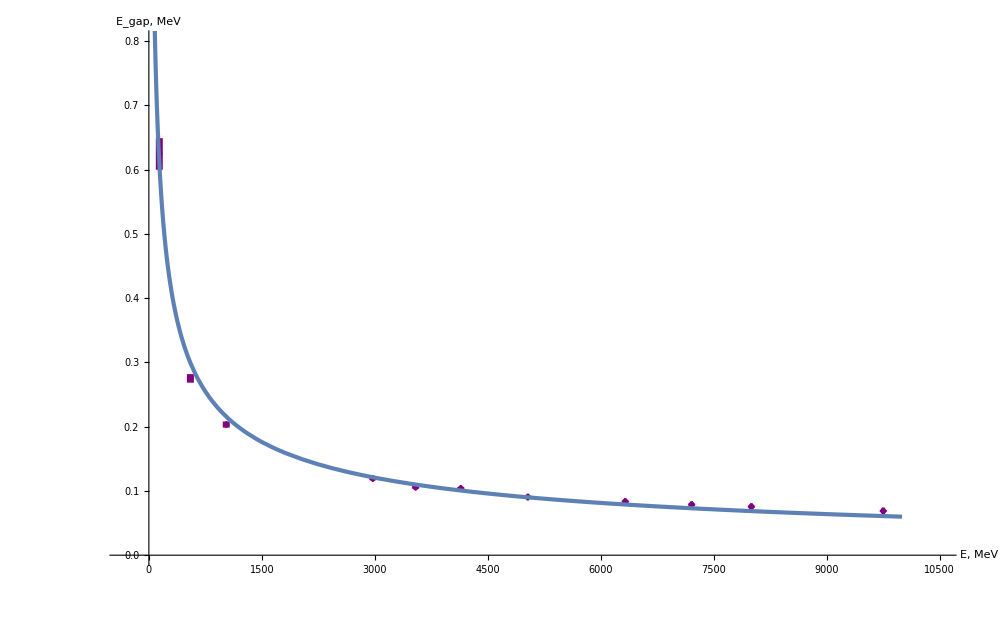

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/re.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.8}}], 
Plot[fitR["Function"]@x,{x,0,10000}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/re.png",plotR,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
expR= {fitR[10^20],fitR[1]-fitR[10^20]};
expR//TableForm
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_re_res.csv",exp,"CSV"]
```

-0.0135181
7.34727

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_re_res.csv

```mathematica
fitR[10^20]
```

-0.0168216